1. vaje: Osnove Mathematice

1. S pomočjo mathematice izračunaj:

```mathematica
(1/3+1/6)^2
```

1/4

```mathematica
3/(6/8)
```

4

```mathematica
Sin[Pi/2]
```

1

```mathematica
ⅇ^Log[7]
```

7

2. Poenostavi naslednje izraze:

```mathematica
FullSimplify[((3+4x)/(2+5x))^2+((2+x)/(1-x))^2]
```

(2+x)^2/(-1+x)^2+(3+4 x)^2/(2+5 x)^2

```mathematica
FullSimplify[x/y+y/x+2]
```

(x+y)^2/(x y)

```mathematica
Simplify[(x^2+y^2)^2-2(xy)^2]
```

-2 xy^2+(x^2+y^2)^2

```mathematica
Simplify[Sin[x]^2+Cos[x]^2]
```

1

```mathematica
Simplify[2Sin[x]* Cos[x]]
```

Sin[2 x]

```mathematica
FullSimplify[(Tan[π/8])^4+ (Ctg[π/8])^4]
```

Ctg[π/8]^4+Tan[π/8]^4

3. Razstavi izraz

```mathematica
TrigExpand[ (x+xy+y)^10]
```

x^10+10 x^9 xy+45 x^8 xy^2+120 x^7 xy^3+210 x^6 xy^4+252 x^5 xy^5+210 x^4 xy^6+120 x^3 xy^7+45 x^2 xy^8+10 x xy^9+xy^10+10 x^9 y+90 x^8 xy y+360 x^7 xy^2 y+840 x^6 xy^3 y+1260 x^5 xy^4 y+1260 x^4 xy^5 y+840 x^3 xy^6 y+360 x^2 xy^7 y+90 x xy^8 y+10 xy^9 y+45 x^8 y^2+360 x^7 xy y^2+1260 x^6 xy^2 y^2+2520 x^5 xy^3 y^2+3150 x^4 xy^4 y^2+2520 x^3 xy^5 y^2+1260 x^2 xy^6 y^2+360 x xy^7 y^2+45 xy^8 y^2+120 x^7 y^3+840 x^6 xy y^3+2520 x^5 xy^2 y^3+4200 x^4 xy^3 y^3+4200 x^3 xy^4 y^3+2520 x^2 xy^5 y^3+840 x xy^6 y^3+120 xy^7 y^3+210 x^6 y^4+1260 x^5 xy y^4+3150 x^4 xy^2 y^4+4200 x^3 xy^3 y^4+3150 x^2 xy^4 y^4+1260 x xy^5 y^4+210 xy^6 y^4+252 x^5 y^5+1260 x^4 xy y^5+2520 x^3 xy^2 y^5+2520 x^2 xy^3 y^5+1260 x xy^4 y^5+252 xy^5 y^5+210 x^4 y^6+840 x^3 xy y^6+1260 x^2 xy^2 y^6+840 x xy^3 y^6+210 xy^4 y^6+120 x^3 y^7+360 x^2 xy y^7+360 x xy^2 y^7+120 xy^3 y^7+45 x^2 y^8+90 x xy y^8+45 xy^2 y^8+10 x y^9+10 xy y^9+y^10

```mathematica
TrigExpand[Sin[x+y]]
```

Cos[y] Sin[x]+Cos[x] Sin[y]

4.  naloga

```mathematica
a=3
b=4
c=6
o=a+b+c
s=o/2
FullSimplify[√(s*(s-a)*(s-b)*(s-c))]
```

3

4

6

13

13/2

(√455)/4

5. Naloga

```mathematica
s = {3, 2, 0,0,5,13,2,-x,8}
s[[5]]
s[[-1]]
```

{3,2,0,0,5,13,2,-x,8}

5

8

6. naloga

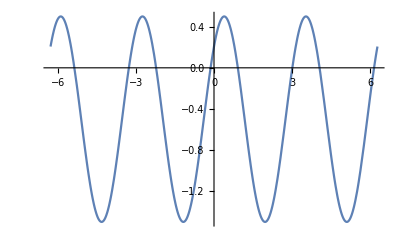

```mathematica
Plot[Sin[2x+π/4]-1/2, {x, -2π,2π}]
```

7. naloga

-5 Sin[2-x]

-6+2^x

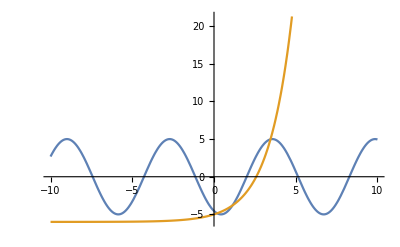

```mathematica
f [x]=5*Sin[x-2]
g[x]= 2^x-6
Plot[{f[x],g[x]},{x, -10,10}]
```

8. naloga

```mathematica
a = 3^200+20
b  =2^300+30
a==b
```

265613988875874769338781322035779626829233452653394495974574961739092490901302182994384699044021

2037035976334486086268445688409378161051468393665936250636140449354381299763336706183397406

False

```mathematica
a<b
```

False

```mathematica
a >b
```

True

9. naloga

```mathematica
f[x]= x^2+4x+2
Solve[f[x]== 0]
```

2+4 x+x^2

{{x→-2-√2},{x→-2+√2}}

```mathematica
g[x]= x^2+4x+5
Solve[g[x]==0]
```

5+4 x+x^2

{{x→-2-ⅈ},{x→-2+ⅈ}}

10. Naloga

```mathematica
Reduce[x^4== 1]
```

x==-1||x==-ⅈ||x==ⅈ||x==1

11. naloga

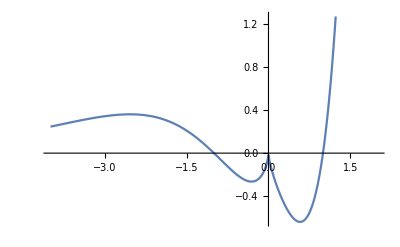

```mathematica
f[x]=(x^2-(x^2)^(1/3))ⅇ^x
Plot[f[x],{x,-4,2}]
```

```mathematica
Solve[f[x]==0]
```

{{x→0},{x→1}}

```mathematica
Reduce[f[x]==0]
```

x==-1||x==0||x==1